```mathematica
546512131006/146642391445//N
```

3.72684

```mathematica
546512131006
```

```mathematica
UnitConvert[1/(SemanticInterpretation["23.4 MiB"]/(Quantity[1,"Minutes"]+Quantity[48,"Seconds"]))*Quantity[546512131006,"Bytes"],MixedUnit[{"Days","Hours","Minutes","Seconds"}]]
```

27 20

```mathematica
UnitConvert[1/(SemanticInterpretation["145.6 MiB"]/(Quantity[1,"Minutes"]+Quantity[6,"Seconds"]))*Quantity[546512131006,"Bytes"],MixedUnit[{"Days","Hours","Minutes","Seconds"}]]
```

2 17

```mathematica
GeoListPlot[GeoPositionXYZ[SpherePoints[10000],1],GeoProjection->"WinkelTripel"]
```

-Graphics-

```mathematica
removeAltitude[gp_]:=GeoPosition[GeoPosition[gp][[1,;;2]]]
```

```mathematica
GeoVoronoi[ps_]:=Module[{chm,coords,verts},chm=ConvexHullMesh[GeoPositionXYZ[ps][[1]]];
coords=MeshCoordinates[chm];
verts=removeAltitude/@Thread[GeoPositionXYZ[Cross[coords[[#2]]-coords[[#1]],coords[[#3]]-coords[[#1]]]&@@@MeshCells[chm,2][[All,1]]]];
GeoPolygon[verts[[#]]]&/@DualPolyhedron[chm][[2]]]
GeoVoronoi[ps_GeoPosition]:=GeoVoronoi[Thread[ps]]
```

```mathematica
ps=GeoPosition@GeoPositionXYZ[SpherePoints[1000]*QuantityMagnitude[Entity["Planet","Earth"][EntityProperty["Planet","Radius"]], "Meters"]];
```

```mathematica
GeoGraphics[{{GeoStyling[Opacity[0.6]],RandomColor[],#}&/@GeoVoronoi[ps],Red,PointSize[Large],Point[ps]},GeoRange->"World"]
```

-Graphics-

```mathematica
ResourceFunction["GeoGraphics3D"][{{GeoStyling[Opacity[0.6]],RandomColor[],#}&/@GeoVoronoi[ps],Red,PointSize[Large],Point[ps]}]
```

-Graphics3D-

```mathematica
Graphics3D/@NestList[AugmentedPolyhedron[#,0]&,CanonicalizePolyhedron[Icosahedron[]],3]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Graphics3D@AugmentedPolyhedron[CanonicalizePolyhedron[Icosahedron[]],0]
```

-Graphics3D-

```mathematica
Icosahedron[{0,0,0}]
```

Icosahedron[{0,0,0}]

```mathematica
poly1=GeodesicPolyhedron[6]
```

Polyhedron[…]

```mathematica
poly2=DualPolyhedron[poly1]
```

Polyhedron[…]

```mathematica
RegionIntersection[VoronoiMesh@PolyhedronCoordinates[GeodesicPolyhedron[2]],Ball[]]
```

BooleanRegion[#1&&#2&,{-Graphics3D-,Ball[{0,0,0}]}]

```mathematica
ps=GeoPosition[GeoPositionXYZ[PolyhedronCoordinates[poly1]*QuantityMagnitude[Entity["Planet","Earth"][EntityProperty["Planet","Radius"]], "Meters"]]];
```

```mathematica
ps=GeoPosition[GeoPositionXYZ[SpherePoints[Length[PolyhedronCoordinates[poly1]]]*QuantityMagnitude[Entity["Planet","Earth"][EntityProperty["Planet","Radius"]], "Meters"]]];
```

```mathematica
GeoListPlot@ps
```

-Graphics-

```mathematica
GeoVoronoi[ps_]:=Module[{chm,coords,verts},chm=ConvexHullMesh[GeoPositionXYZ[ps][[1]]];
coords=MeshCoordinates[chm];
verts=removeAltitude/@Thread[GeoPositionXYZ[Cross[coords[[#2]]-coords[[#1]],coords[[#3]]-coords[[#1]]]&@@@MeshCells[chm,2][[All,1]]]];
GeoPolygon[verts[[#]]]&/@DualPolyhedron[chm][[2]]]
GeoVoronoi[ps_GeoPosition]:=GeoVoronoi[Thread[ps]]
```

```mathematica
voronoi=GeoVoronoi[ps];
```

```mathematica
GeoGraphics[{{GeoStyling[Opacity[0.6]],RandomColor[],#}&/@voronoi,Red,PointSize[Large],Point[ps]},GeoRange->"World"]
```

-Graphics-

```mathematica
GeoGraphics[{{GeoStyling[Opacity[0.6]],RandomColor[],#}&/@voronoi,Red,PointSize[Large],Point[ps]},GeoRange->"World"]
```

-Graphics-

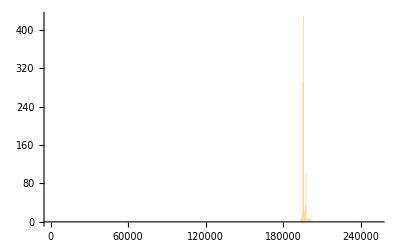

```mathematica
Histogram[GeoArea/@voronoi,PlotRange->{{0,All},All}]
```

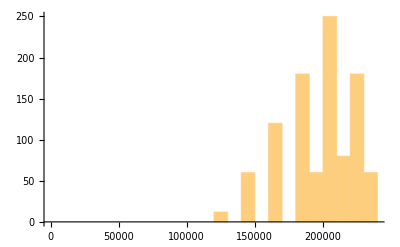

```mathematica
Histogram[GeoArea/@voronoi,PlotRange->{{0,All},All}]
```

```mathematica
ResourceFunction["GeoGraphics3D"][{{GeoStyling[Opacity[0.6]],RandomColor[],#}&/@voronoi,Red,PointSize[Large],Point[ps]}]
```

-Graphics3D-

```mathematica
rawTSV=StringSplit[StringSplit["gbifID\tdatasetKey\toccurrenceID\tkingdom\tphylum\tclass\torder\tfamily\tgenus\tspecies\tinfraspecificEpithet\ttaxonRank\tscientificName\tverbatimScientificName\tverbatimScientificNameAuthorship\tcountryCode\tlocality\tstateProvince\toccurrenceStatus\tindividualCount\tpublishingOrgKey\tdecimalLatitude\tdecimalLongitude\tcoordinateUncertaintyInMeters\tcoordinatePrecision\televation\televationAccuracy\tdepth\tdepthAccuracy\teventDate\tday\tmonth\tyear\ttaxonKey\tspeciesKey\tbasisOfRecord\tinstitutionCode\tcollectionCode\tcatalogNumber\trecordNumber\tidentifiedBy\tdateIdentified\tlicense\trightsHolder\trecordedBy\ttypeStatus\testablishmentMeans\tlastInterpreted\tmediaType\tissue
133354851\t4fa7b334-ce0d-4e88-aaae-2e0c138d049e\tURN:catalog:CLO:EBIRD:OBS19346318\tAnimalia\tChordata\tAves\tPelecaniformes\tArdeidae\tEgretta\tEgretta tricolor\t\tSPECIES\tEgretta tricolor (Statius Muller, 1776)\tEgretta tricolor\t\tUS\tBrazoria County Texas\tTexas\tPRESENT\t\te2e717bf-551a-4917-bdc9-4fa0f342c530\t29.213955\t-95.40584\t\t\t\t2002-01-20T00:00:00\t20\t1\t2002\t2480881\t2480881\tHUMAN_OBSERVATION\tCLO\tEBIRD\tOBS19346318\t\t\t\tCC_BY_4_0\t\tobsr33483\t\t\t2023-01-24T14:56:25.836Z\t\tCONTINENT_DERIVED_FROM_COORDINATES
138165906\t4fa7b334-ce0d-4e88-aaae-2e0c138d049e\tURN:catalog:CLO:EBIRD:OBS22331383\tAnimalia\tChordata\tAves\tPasseriformes\tPolioptilidae\tPolioptila\tPolioptila caerulea\t\tSPECIES\tPolioptila caerulea (Linnaeus, 1766)\tPolioptila caerulea\t\tUS\t**HUNTLEY MEADOWS PARK\tVirginia\tPRESENT\t\te2e717bf-551a-4917-bdc9-4fa0f342c530\t38.757645\t-77.09841\t\t\t\t2004-06-26T00:00:00\t26\t6\t2004\t2487596\t2487596\tHUMAN_OBSERVATION\tCLO\tEBIRD\tOBS22331383\t\t\t\tCC_BY_4_0\t\tobsr41831\t\t\t2023-01-24T14:56:26.457Z\t\tCONTINENT_DERIVED_FROM_COORDINATES
140627465\t4fa7b334-ce0d-4e88-aaae-2e0c138d049e\tURN:catalog:CLO:EBIRD:OBS25737962\tAnimalia\tChordata\tAves\tColumbiformes\tColumbidae\tZenaida\tZenaida macroura\t\tSPECIES\tZenaida macroura (Linnaeus, 1758)\tZenaida macroura\t\tUS\tMogadore Reservoir--East End\tOhio\tPRESENT\t\te2e717bf-551a-4917-bdc9-4fa0f342c530\t41.06719\t-81.307755\t\t\t\t2005-05-01T00:00:00\t1\t5\t2005\t2495347\t2495347\tHUMAN_OBSERVATION\tCLO\tEBIRD\tOBS25737962\t\t\t\tCC_BY_4_0\t\tobsr18443\t\t\t2023-01-24T14:56:16.368Z\t\tCONTINENT_DERIVED_FROM_COORDINATES
128826491\t4fa7b334-ce0d-4e88-aaae-2e0c138d049e\tURN:catalog:CLO:EBIRD:OBS26795183\tAnimalia\tChordata\tAves\tAnseriformes\tAnatidae\tAix\tAix sponsa\t\tSPECIES\tAix sponsa (Linnaeus, 1758)\tAix sponsa\t\tUS\tHughes Hollow - McKee Beshers WMA\tMaryland\tPRESENT\t3\te2e717bf-551a-4917-bdc9-4fa0f342c530\t39.080376\t-77.40351\t\t\t\t\t\t2005-10-24T00:00:00\t24\t10\t2005\t2498387\t2498387\tHUMAN_OBSERVATION\tCLO\tEBIRD\tOBS26795183\t\t\t\tCC_BY_4_0\t\tobsr44100\t\t\t2023-01-24T14:56:46.513Z\t\tCONTINENT_DERIVED_FROM_COORDINATES
","\n"],"\t"];
```

```mathematica
rawTSV[[All,23]]
```

{decimalLongitude,-95.40584,-77.09841,-81.307755,-77.40351}

```mathematica
Grid[MapIndexed[{First[#2]-1,#1}&,rawTSV[[1]]],Alignment->Left]
```

0 | gbifID
1 | datasetKey
2 | occurrenceID
3 | kingdom
4 | phylum
5 | class
6 | order
7 | family
8 | genus
9 | species
10 | infraspecificEpithet
11 | taxonRank
12 | scientificName
13 | verbatimScientificName
14 | verbatimScientificNameAuthorship
15 | countryCode
16 | locality
17 | stateProvince
18 | occurrenceStatus
19 | individualCount
20 | publishingOrgKey
21 | decimalLatitude
22 | decimalLongitude
23 | coordinateUncertaintyInMeters
24 | coordinatePrecision
25 | elevation
26 | elevationAccuracy
27 | depth
28 | depthAccuracy
29 | eventDate
30 | day
31 | month
32 | year
33 | taxonKey
34 | speciesKey
35 | basisOfRecord
36 | institutionCode
37 | collectionCode
38 | catalogNumber
39 | recordNumber
40 | identifiedBy
41 | dateIdentified
42 | license
43 | rightsHolder
44 | recordedBy
45 | typeStatus
46 | establishmentMeans
47 | lastInterpreted
48 | mediaType
49 | issue

```mathematica
ps=GeoPositionXYZ[Import["~/git/ecosystem_dimension_reduction/input_files/10000SpherePoints.csv"]*QuantityMagnitude[Entity["Planet","Earth"][EntityProperty["Planet","Radius"]], "Meters"]];
```

```mathematica
MapAt[#+1&,cellCounts,{All,1}]
```

```mathematica
GeoListPlot@GeoPositionXYZ[Thread[ps][[Keys[Select[cellCounts,#[[2]]>1000&]]+1]]]
```

-Graphics-

```mathematica
SparseArray[MapAt[#+1&,cellCounts,{All,1}],Length[Thread[ps]]]
```

SparseArray[…]

```mathematica
GeoRegionValuePlot[Thread[Thread[GeoPosition@ps]->Normal@SparseArray[MapAt[#+1&,cellCounts,{All,1}],Length[Thread[ps]]]]]
```

-Graphics-

```mathematica
GeoListPlot[ps]
```

-Graphics-